# Decision boundary

```mathematica
f[fbase_, steps_, L_, r_, delta_] = (L - 1 - r * Sum[((delta/(1+r))^t)*(fbase * L - fbase * t),{t, 1,steps}])/(L - 1 - r * Sum[((delta/(1+r))^t)*(L - t),{t, 1,steps}])
```

(-1+L-(delta fbase r (-1+L-delta L-r+L r+(delta/(1+r))^steps-L (delta/(1+r))^steps+delta L (delta/(1+r))^steps+r (delta/(1+r))^steps-L r (delta/(1+r))^steps+(delta/(1+r))^steps steps-delta (delta/(1+r))^steps steps+r (delta/(1+r))^steps steps))/(-1+delta-r)^2)/(-1+L-(delta r (-1+L-delta L-r+L r+(delta/(1+r))^steps-L (delta/(1+r))^steps+delta L (delta/(1+r))^steps+r (delta/(1+r))^steps-L r (delta/(1+r))^steps+(delta/(1+r))^steps steps-delta (delta/(1+r))^steps steps+r (delta/(1+r))^steps steps))/(-1+delta-r)^2)

50

{{1.,0.988806,0.978602,0.969403,0.96119,0.953923,0.947545,0.941987,0.937175,0.933031,0.92948,0.926451,0.923878,0.921698,0.919858,0.918309,0.917007,0.915917,0.915005,0.914245,0.913611,0.913084,0.912647,0.912284,0.911985,0.911738,0.911534,0.911366,0.911229,0.911116,0.911024,0.910949,0.910888,0.910839,0.910799,0.910767,0.910742,0.910721,0.910705,0.910692,0.910683,0.910675,0.910669,0.910665,0.910662,0.910659,0.910658,0.910657,0.910656,0.910656,0.910656},{1.,0.977612,0.957205,0.938805,0.922379,0.907846,0.89509,0.883975,0.87435,0.866062,0.858961,0.852903,0.847755,0.843396,0.839716,0.836617,0.834015,0.831834,0.830011,0.828489,0.827222,0.826168,0.825294,0.824569,0.82397,0.823475,0.823067,0.822732,0.822457,0.822232,0.822048,0.821898,0.821776,0.821678,0.821598,0.821534,0.821483,0.821442,0.82141,0.821385,0.821365,0.82135,0.821338,0.82133,0.821323,0.821319,0.821316,0.821314,0.821312,0.821312,0.821312},{1.,0.966418,0.935807,0.908208,0.883569,0.861769,0.842636,0.825962,0.811524,0.799093,0.788441,0.779354,0.771633,0.765094,0.759574,0.754926,0.751022,0.747751,0.745016,0.742734,0.740833,0.739252,0.73794,0.736853,0.735955,0.735213,0.734601,0.734098,0.733686,0.733348,0.733072,0.732847,0.732665,0.732517,0.732397,0.732301,0.732225,0.732164,0.732115,0.732077,0.732048,0.732025,0.732008,0.731994,0.731985,0.731978,0.731973,0.73197,0.731969,0.731968,0.731968},{1.,0.955224,0.91441,0.87761,0.844758,0.815692,0.790181,0.76795,0.748699,0.732123,0.717921,0.705806,0.69551,0.686792,0.679431,0.673234,0.668029,0.663668,0.660022,0.656978,0.654444,0.652336,0.650587,0.649138,0.647939,0.64695,0.646135,0.645464,0.644914,0.644464,0.644096,0.643796,0.643553,0.643356,0.643197,0.643069,0.642966,0.642885,0.64282,0.64277,0.64273,0.6427,0.642677,0.642659,0.642646,0.642637,0.642631,0.642627,0.642625,0.642624,0.642624}}

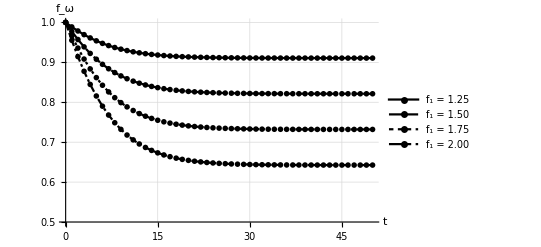

```mathematica
layers = 50
data = Table[Table[f[factor,x,layers,0.05,0.9], {x,0,layers,1}], {factor, 1.25, 2., 0.25}]
ListLinePlot[data, PlotTheme->"Monochrome", PlotRange -> {0.5, 1}, AxesLabel->{"t", "f_ω"}, PlotLegends->{"f_1 = 1.25", "f_1 = 1.50", "f_1 = 1.75", "f_1 = 2.00"}, GridLines->Automatic, DataRange->{0, layers}]
```